```mathematica
(* deletes duplicate pairs from list of predicted edges *)
deleteduplicatepairs[pairs_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
Delete[pairs,todelete]];

(* brute force method for computing effective transition method for link prediction *)
bruteEffectiveTransition[G_,k_]:=
Module[{M,spec,R,prediction, n, range, cutoff},
range = VertexList[G];
n = VertexCount[G];
M=AdjacencyMatrix[G];spec=N[Max[Abs[Eigenvalues[M]]]];R=RandomReal[{0,1},{n,n}];
For[i=1,i≤n,i++,For[j=i+1,j≤n,j++,R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=2,i≤n,i++,
For[j=1,j≤i-1,j++, R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=1,i≤n,i++,
R[[i]][[i]]=0;];

cutoff = TakeLargest[Flatten[R-10M],2*k][[2*k]];
deleteduplicatepairs[Position[R-10M,_?(#≥ cutoff&)]]];

(* recursive algorithm for computing effective transition *)
recursiveEffectiveTransition[G_,k_]:=
Module[{A,size,vertexes,scores,R,spec,cutoff},

(* the recursion, breaks down matrix to avoid computing inverses *)
simplify[M_, nodes_, pos_]:=
Module[{n, part1,part2,part3,M1,M2,M3, labels,labels1,labels2,labels3},
n = Length[nodes];
labels = Range[n];
labels1 = labels[[1;;n-1]];
labels2 = labels[[2;;n]];
labels3 = Append[labels[[3;;n]],labels[[1]]];
part1 = nodes[[1;;n-1]];
part2 = nodes[[2;;n]];
part3 = Append[nodes[[3;;n]],nodes[[1]]];
M1 = M[[labels1,labels1]]-M[[labels1,Complement[labels,labels1]]].Inverse[M[[Complement[labels,labels1],Complement[labels,labels1]]] - spec].M[[Complement[labels,labels1],labels1]];
M2 = M[[labels2,labels2]]-M[[labels2,Complement[labels,labels2]]].Inverse[M[[Complement[labels,labels2],Complement[labels,labels2]]] - spec].M[[Complement[labels,labels2],labels2]];
M3 = M[[labels3,labels3]]-M[[labels3,Complement[labels,labels3]]].Inverse[M[[Complement[labels,labels3],Complement[labels,labels3]]] - spec].M[[Complement[labels,labels3],labels3]]; 
If[n == 3, {R[[part1[[1]]]][[part1[[2]]]],R[[part2[[1]]]][[part2[[2]]]],R[[part3[[1]]]][[part3[[2]]]]} = {M1[[1]][[2]],M2[[1]][[2]],M3[[1]][[2]]}];
If[n > 3, simplify[M1,part1,1] && simplify[M2,part2,2] && simplify[M3,part3,3]];
];

A = AdjacencyMatrix[G];
vertexes = VertexList[G];
size = Length[vertexes];
scores = ConstantArray[0,{size,size}];
R = scores;
spec = N[Max[Abs[Eigenvalues[A]]]];
simplify[A,vertexes,1];
cutoff = TakeLargest[Flatten[R-10A],2*k][[2*k]];
deleteduplicatepairs[Position[R-10A,_?(#≥cutoff&)]]];

(* more optimized recursive algorithm for effective transition *)
speedyEffectiveTransition[G_,k_]:=
Module[{A,size,vertexes,scores,R,spec,cutoff},

(* the recursion, breaks down matrix to avoid computing inverses *)
simplify[M_, nodes_, pos_]:=
Module[{n, part1,part2,part3,M1,M2,M3, labels,labels1,labels2,labels3},
n = Length[nodes];
labels = Range[n];
labels1 = labels[[1;;n-1]];
labels2 = labels[[2;;n]];
labels3 = Append[labels[[3;;n]],labels[[1]]];
part1 = nodes[[1;;n-1]];
part2 = nodes[[2;;n]];
part3 = Append[nodes[[3;;n]],nodes[[1]]];
M1 = M[[labels1,labels1]]-M[[labels1,Complement[labels,labels1]]].Inverse[M[[Complement[labels,labels1],Complement[labels,labels1]]] - spec].M[[Complement[labels,labels1],labels1]];
M2 = M[[labels2,labels2]]-M[[labels2,Complement[labels,labels2]]].Inverse[M[[Complement[labels,labels2],Complement[labels,labels2]]] - spec].M[[Complement[labels,labels2],labels2]];
M3 = M[[labels3,labels3]]-M[[labels3,Complement[labels,labels3]]].Inverse[M[[Complement[labels,labels3],Complement[labels,labels3]]] - spec].M[[Complement[labels,labels3],labels3]];
If[n == 3, If[pos ==1, {R[[part1[[1]]]][[part1[[2]]]],R[[part2[[1]]]][[part2[[2]]]],R[[part3[[1]]]][[part3[[2]]]]} = {M1[[1]][[2]],M2[[1]][[2]],M3[[1]][[2]]}, If[pos ==2,{R[[part2[[1]]]][[part2[[2]]]],R[[part3[[1]]]][[part3[[2]]]]} = {M2[[1]][[2]],M3[[1]][[2]]}],If[pos==3,R[[part2[[1]]]][[part2[[2]]]] = M2[[1]][[2]]]]];
If[n > 3, If[pos==1,simplify[M1,part1,1] && simplify[M2,part2,2] && simplify[M3,part3,3],If[pos==2,simplify[M2,part2,2] && simplify[M3,part3,3],If[pos==3,simplify[M2,part2,2] ]]]];
];

A = AdjacencyMatrix[G];
vertexes = VertexList[G];
size = Length[vertexes];
scores = ConstantArray[0,{size,size}];
R = scores;
spec = N[Max[Abs[Eigenvalues[A]]]];
simplify[A,vertexes,1];
cutoff = TakeLargest[Flatten[R-10A],2*k][[2*k]] ;
deleteduplicatepairs[Position[R-10A,_?(#≥cutoff&)]]];
```

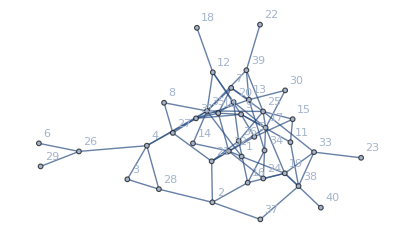

```mathematica
graph = RandomGraph[{40,75},VertexLabels->Automatic]
```

```mathematica
Timing[bruteEffectiveTransition[graph,5]]
Timing[speedyEffectiveTransition[graph,3]]
```

{0.348263,{{1,14},{5,11},{6,29},{18,22},{18,40}}}

{139400.,{{6,29},{18,22},{18,40}}}

```mathematica
scores = bruteEffectiveTransition[graph,5]
```

{{0,1.84514,1.84103,0.917792,2.21518,0.493985,0.125919,1.82639,0.496274,2.13,1.466,2.47443,2.13294,1.36109,1.62246},{1.84514,0,1.65305,1.26673,1.69689,0.707907,0.184121,1.9377,0.711953,1.84514,1.70496,1.73589,1.4664,1.6788,1.92356},{1.84103,1.65305,0,0.82149,1.75644,0.411529,0.104109,2.36539,0.413267,1.84103,1.33987,2.1654,2.14937,1.44416,1.95504},{0.917792,1.26673,0.82149,0,0.607195,1.52472,0.467314,0.731166,1.54583,0.917792,1.5289,0.833356,0.619199,2.0401,1.57577},{2.21518,1.69689,1.75644,0.607195,0,0.316661,0.0800468,2.22739,0.317985,2.21518,1.0415,2.26897,2.38645,0.955354,1.26553},{0.493985,0.707907,0.411529,1.52472,0.316661,0,1.,0.372528,2.06965,0.493985,1.,0.440487,0.322051,1.0155,0.730724},{0.125919,0.184121,0.104109,0.467314,0.0800468,1.,0,0.0943122,0.944896,0.125919,0.234742,0.112137,0.0806476,0.265738,0.190499},{1.82639,1.9377,2.36539,0.731166,2.22739,0.372528,0.0943122,0,0.374116,1.82639,1.20149,1.84356,2.27959,1.14785,1.78592},{0.496274,0.711953,0.413267,1.54583,0.317985,2.06965,0.944896,0.374116,0,0.496274,1.,0.442497,0.323231,1.02163,0.734992},{2.13,1.84514,1.84103,0.917792,2.21518,0.493985,0.125919,1.82639,0.496274,0,1.466,2.47443,2.13294,1.36109,1.62246},{1.466,1.70496,1.33987,1.5289,1.0415,1.,0.234742,1.20149,1.,1.466,0,1.32727,1.20763,2.31551,1.72274},{2.47443,1.73589,2.1654,0.833356,2.26897,0.440487,0.112137,1.84356,0.442497,2.47443,1.32727,0,1.91505,1.27912,1.57524},{2.13294,1.4664,2.14937,0.619199,2.38645,0.322051,0.0806476,2.27959,0.323231,2.13294,1.20763,1.91505,0,1.01861,1.32501},{1.36109,1.6788,1.44416,2.0401,0.955354,1.0155,0.265738,1.14785,1.02163,1.36109,2.31551,1.27912,1.01861,0,1.88122},{1.62246,1.92356,1.95504,1.57577,1.26553,0.730724,0.190499,1.78592,0.734992,1.62246,1.72274,1.57524,1.32501,1.88122,0}}

```mathematica
s = Flatten[scores];
Length[s]
```

225

```mathematica
TakeLargest[s, 5]
```

{2.47443,2.47443,2.47443,2.47443,2.38645}

```mathematica
Position[scores, _?(#≥ 2.38640&)]
```

{{1,12},{5,13},{10,12},{12,1},{12,10},{13,5}}